## static solution

### the function for solving the static equations

#### Static equations and the asymptotic expansion at the horizon

```mathematica
b=-35.0;Q=0.448;
```

```mathematica
f[x_]=1/(1+b x^2);
eqdζdr=ζ'[r]-(Q^2/(2 r^3 f[ϕ[r]] ζ[r])-ζ[r]/(2 r)+r/2(1/ζ[r]-ζ[r] )ϕ'[r]^2);
eqdϕdr=ϕ''[r]-((-(Q^2 f'[ϕ[r]])/(2 r^4 f[ϕ[r]]^2))/(1-ζ[r]^2)+(2 ζ[r] ζ'[r] ϕ'[r])/(1-ζ[r]^2)- (2/r +r ϕ'[r]^2) ϕ'[r]);(* The constraint equations used to solve for ζ and ϕ *)


BCHϕr[ϕh_,r_]=ϕh+(Q^2 f'[ϕh] (r-rh))/(2 Q^2 rh f[ϕh]-2 rh^3 f[ϕh]^2)+(Q^2 f'[ϕh] ((Q^2-2 rh^2 f[ϕh]) (4 f[ϕh]^2 (Q^2-rh^2 f[ϕh])+Q^2 f'[ϕh]^2)+Q^2 f[ϕh] (-Q^2+rh^2 f[ϕh]) f''[ϕh]) (r-rh)^2)/(16 rh^2 f[ϕh]^3 (-Q^2+rh^2 f[ϕh])^3);(*scalar field near‑horizon expansion*)


BCHζr[ϕh_,r_]=1+((-rh^2+Q^2/f[ϕh]) (r-rh))/(2 rh^3)+((6 rh^4+(Q^2 (-2 f[ϕh] (Q^2+6 rh^2 f[ϕh])-(3 Q^2 rh^2 f'[ϕh]^2)/(Q^2-rh^2 f[ϕh])))/f[ϕh]^3) (r-rh)^2)/(16 rh^6);(*metric near‑horizon expansion*)
```

#### The function for solving the static equations

```mathematica
ϵ=10^-7;INF=10^7;rhϵ=rh+ϵ;nn=30;
Off[NDSolve::precw];
ζϕr[ϕh_?NumberQ]:={ζ,ϕ}/.NDSolve[{eqdζdr==0, eqdϕdr==0,
ζ[rhϵ]==BCHζr[ϕh,rhϵ],
(*ζ'[rhϵ]==D[BCHζr[ϕh,r],r]/.r->rhϵ,*)
ϕ[rhϵ]==BCHϕr[ϕh,rhϵ],
ϕ'[rhϵ] ==D[BCHϕr[ϕh,r],r]/.r->rhϵ},
 {ζ,ϕ},{r, rhϵ,INF},WorkingPrecision->nn,PrecisionGoal->nn][[1]]

ϕr[ϕh_?NumberQ]:=ϕ/.NDSolve[{eqdζdr==0, eqdϕdr==0,
ζ[rhϵ]==BCHζr[ϕh,rhϵ],
(*ζ'[rhϵ]==D[BCHζr[ϕh,r],r]/.r->rhϵ,*)
ϕ[rhϵ]==BCHϕr[ϕh,rhϵ],
ϕ'[rhϵ] == D[BCHϕr[ϕh,r],r]/.r->rhϵ},
 {ζ,ϕ},{r, rhϵ,INF},WorkingPrecision->nn,PrecisionGoal->nn][[1]]
```

#### The shooting‑method routine and its testing

```mathematica
ϕINF[ϕh_]:=ϕr[ϕh][INF];
ϕHshoot[phihSeed_] :=
ϕh/.FindRoot[ϕINF[ϕh]==10^-7, {ϕh,phihSeed}, WorkingPrecision->nn,PrecisionGoal->nn]
```

### Computing the charge‑to‑mass ratio using the shooting method

```mathematica
rhlist={};entropylist={};phiHlist={};ADMlist={};Qslist={};qlist={};Slist={};
```

#### Solving the equations in an iterative loop

```mathematica
ϕh0=-10944.8/10000; 
targetPhi=1/Sqrt[-b]; (*evaluating ϕ along the divergent line*)

Monitor[For[rh=15960/10000,rh>120000/100000,rh=rh-1/1000,
{phiH=Rationalize[ϕHshoot[ϕh0]];
ζϕrsol=ζϕr[phiH];
ADM=INF/2((ζϕrsol[[1]])[INF])^2;
Qs=-(ζϕrsol[[2]])'[INF] INF^2;
q=Q/ADM;

If[Abs[phiH+targetPhi]<0.01,Print["q at \!\(\*SuperscriptBox[\(b\), \(\(-1\)/2\)]\) = ",1. q]];(*check if the current ϕh is sufficiently close to the target*)
AppendTo[rhlist,1. rh];
AppendTo[entropylist,1. π rh^2];
AppendTo[phiHlist,phiH];
AppendTo[ADMlist,ADM];
AppendTo[Qslist,Qs];
AppendTo[qlist,1. q];
AppendTo[Slist,1.(π rh^2)/(4π ADM^2)]; 
ϕh0=phiH;}],1.{rh,ADM,(π rh^2)/(4π ADM^2),phiH,Qs,q}]
```

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

Divide::infy: 碰到无穷表达式 1/0.

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

FindRoot::jsing: 在点 {ϕh} = {-1.16745905981566922038617738062} 碰到奇异雅克比. 尝试扰动初始点.

General::munfl: 1. 2.×10^-352 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

Divide::infy: 碰到无穷表达式 1/0.

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

FindRoot::jsing: 在点 {ϕh} = {-1.16745905981566805292711756495} 碰到奇异雅克比. 尝试扰动初始点.

Power::infy: 碰到无穷表达式 1/(0``-175.7148212521831).

Power::infy: 碰到无穷表达式 1/(0``-352.5288523683883).

General::munfl: 1. 4.×10^-360 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

Power::infy: 碰到无穷表达式 1/(0``-177.32886872177363).

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

General::munfl: 1. 9.×10^-359 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::stop: 在本次计算中，General::munfl 的进一步输出将被抑制.

Divide::infy: 碰到无穷表达式 1/0.

General::stop: 在本次计算中，Divide::infy 的进一步输出将被抑制.

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

General::stop: 在本次计算中，Infinity::indet 的进一步输出将被抑制.

FindRoot::jsing: 在点 {ϕh} = {-1.16745905981566688546805774922} 碰到奇异雅克比. 尝试扰动初始点.

General::stop: 在本次计算中，FindRoot::jsing 的进一步输出将被抑制.

$Aborted

## Analysis of the static‑solution data

```mathematica
rhlist;(*horizon radius*)
```

```mathematica
phiHlist;(*the scalar‑field value*)
```

```mathematica
qlist(*the dimensionless charge‑to‑mass ratio*)
```

{0.688663,0.690096,0.691672,0.692824,0.694228,0.695858,0.697055,0.698488,0.699925,0.701382,0.702969,0.704344,0.705758,0.707238,0.708727,0.710228,0.711738,0.713656,0.714775,0.717693,0.717855,0.71967,0.720616,0.722593,0.724129,0.724363,0.727429,0.728938,0.730559,0.732193,0.733836,0.73549,0.737248,0.738829,0.740515,0.742212,0.743919,0.745637,0.747367,0.748504,0.751061,0.752649,0.754399,0.756415,0.758684,0.759795,0.761872,0.763452,0.765299,0.767159,0.769031,0.770916,0.773057,0.774728,0.776843,0.778582,0.780959,7.79855×10^-177,ComplexInfinity,1.15079×10^-180,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,2.16488×10^-179,5.62463×10^-180,ComplexInfinity,ComplexInfinity,ComplexInfinity,3.64939×10^-183,9.36364×10^-181,2.40143×10^-181,1.62258×10^-178,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,9.63723×10^-181,ComplexInfinity,7.33711×10^-181,ComplexInfinity,3.02758×10^-182,ComplexInfinity,ComplexInfinity,ComplexInfinity,6.68755×10^-179,2.88438×10^-182,ComplexInfinity,ComplexInfinity,6.94333×10^-183,2.31339×10^-181,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,3.07918×10^-183,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.65929×10^-179,3.11871×10^-183,ComplexInfinity,ComplexInfinity,ComplexInfinity,5.01657×10^-182,ComplexInfinity,9.19873×10^-184,ComplexInfinity,ComplexInfinity}

```mathematica
rhlist[[57]]
```

1.54

```mathematica
qlist[[57]]
```

0.780959

```mathematica
1.54/(1+1.54)(*change of coordinates*)
```

0.606299

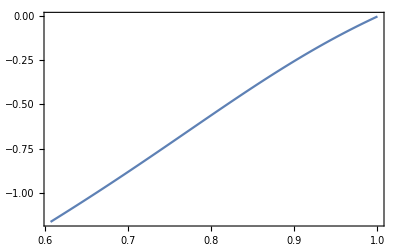

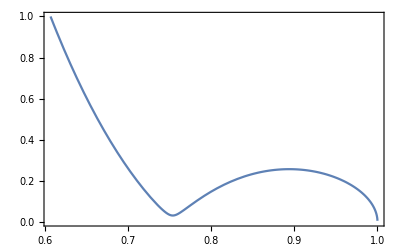

```mathematica
rh=rhlist[[57]];
rhϵ=rh+ϵ;
{ζrsol,ϕrsol}=ζϕr[phiHlist[[57]]];
Plot[ϕrsol[z/(1-z)],{z,0.6062993125984251,0.9999745727088383},Frame->True,PlotRange->All](*scalar‑field profile*)
Plot[ζrsol[z/(1-z)],{z,0.6062993125984251`2,0.9999745727088383},Frame->True,PlotRange->{All,{0,1}}](*metric‑function profile*)
```